```mathematica
(* Automated extraction of parameters from lineage data *)
```

```mathematica
files=FileNames["*.txt","/home/s1402978/Desktop/volume-dep transcription/Analysis_MC4100_25C/MC4100_25C"];
```

```mathematica
data1=Import[#,"CSV",Delimiters->","]&/@files;
```

```mathematica
Length[data1]
```

65

```mathematica
(* Initialize arrays *)
```

```mathematica
data2=Table[0,{i,1,Length[data1]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
data2a=Table[0,{i,1,Length[data1]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
data3a=Table[0,{i,1,Length[data1]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
data3b=Table[0,{i,1,Length[data1]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
CycleLength=Table[0,{i,1,Length[data1]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Lengthincrement=Table[0,{i,1,Length[data1]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
LengthMap=Table[0,{i,1,Length[data1]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
BirthLength=Table[0,{i,1,Length[data1]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
BirthLengthCycleData=Table[0,{i,1,Length[data1]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
DivisionLength=Table[0,{i,1,Length[data1]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
TAcmeans=Table[0,{i,1,Length[data1]}];
TAcvars=Table[0,{i,1,Length[data1]}];
Weighting = Table[0,{i,1,Length[data1]}];
```

```mathematica
(* Format of data is data1[[lineage number]]{timepoint,divisionindicator,length,per-cell total fluorescence intensity,average fluorescence intensity of the mother cell}. 
Extract the first and second moments of protein fluctuations just before and just after cell division; data2a has the ratios of mean before / mean after; data3 has points {z,2*z1} where z is the FF before division and z1 is the FF after division *)
```

```mathematica
data1[[1]]
```

{{1,1,1.5261,216721,4611.09},{2,0,1.68142,227982,4652.69},{3,0,1.53322,211008,4689.07},{4,0,1.49913,206440,4691.82},4760,{4765,0,3.69693,545254,4506.23},{4766,0,3.73892,532946,4594.36},{4767,0,3.80389,551551,4634.88},{4768,0,3.92714,551094,4554.5}}
 |  |  |  |

```mathematica
For[k=1,k≤Length[data1],k++,
(* take in the data into individual arrays *)
DivisionIndicator=Table[data1[[k]][[i]][[2]],{i,1,Length[data1[[k]]]}];FluorescenseData=Table[data1[[k]][[i]][[4]],{i,1,Length[data1[[k]]]}];LengthData=Table[data1[[k]][[i]][[3]],{i,1,Length[data1[[k]]]}];AppVolData=Table[LengthData[[i]](*Pi*0.5^2*),{i,1,Length[data1[[k]]]}](* assume cyclinder units μm^3 *);Concs= Table[FluorescenseData[[i]]/AppVolData[[i]],{i,1,Length[data1[[k]]]}](* prop to conc *);DivisionTimes=DeleteCases[Table[If[DivisionIndicator[[i]]==1,i,0],{i,1,Length[DivisionIndicator]}],0];
(* begin manipulation of the data *)
CycleLength[[k]]=Table[DivisionTimes[[i+1]]-DivisionTimes[[i]],{i,1,Length[DivisionTimes]-1}];TAcmeans[[k]]=Table[Total[Concs[[DivisionTimes[[i]];;DivisionTimes[[i+1]]]]]/(CycleLength[[k]][[i]]),{i,1,Length[DivisionTimes]-1}] (* time-avg means over each generation *);
TAcvars[[k]]=Table[(Total[Concs[[DivisionTimes[[i]];;DivisionTimes[[i+1]]]]^2]-(TAcmeans[[k]][[i]])^2)/(CycleLength[[k]][[i]]),{i,1,Length[DivisionTimes]-1}](* time-avg variances over each generation *);
(*Weighting=Table[,{i,1,Length[DivisionTimes]-1}];*)
Lengthincrement[[k]]=Table[LengthData[[DivisionTimes[[i+1]]-1]]-LengthData[[DivisionTimes[[i]]]],{i,1,Length[DivisionTimes]-1}];LengthMap[[k]]=Table[{LengthData[[DivisionTimes[[i]]]],LengthData[[DivisionTimes[[i+1]]-1]]},{i,1,Length[DivisionTimes]-1}];BirthLength[[k]]=Table[LengthData[[DivisionTimes[[i]]]],{i,1,Length[DivisionTimes]-1}];DivisionLength[[k]]=Table[LengthData[[DivisionTimes[[i+1]]-1]],{i,1,Length[DivisionTimes]-1}];BirthLengthCycleData[[k]]=Table[Table[LengthData[[i]],{i,DivisionTimes[[j]],DivisionTimes[[j+1]]-1}],{j,1,Length[DivisionTimes]-1}];Fluoafterdiv=Table[FluorescenseData[[DivisionTimes[[i]]]],{i,2,Length[DivisionTimes]}];Fluobeforediv=Table[FluorescenseData[[DivisionTimes[[i]]-1]],{i,2,Length[DivisionTimes]}]; z=N[Variance[Fluobeforediv]/Mean[Fluobeforediv]]; z1=N[Variance[Fluoafterdiv]/Mean[Fluoafterdiv]];y=N[Variance[Fluoafterdiv]-(Variance[Fluobeforediv]/4)];x=N[Mean[Fluobeforediv]];If[y≥0,data2[[k]]={z,2*z1},data2[[k]]=0;];
data2a[[k]]=N[Mean[Fluobeforediv]]/N[Mean[Fluoafterdiv]];];data3=DeleteCases[data2,0];
```

```mathematica
CVmeans = Table[Variance[TAcmeans[[i]]]/Mean[TAcmeans[[i]]],{i,1,Length[TAcmeans]}]; (* coefficient of variation for each lineage of the distribution of time averaged means in each cc generation *)
```

```mathematica
CVvars = Table[Variance[TAcvars[[i]]]/Mean[TAcvars[[i]]],{i,1,Length[TAcvars]}]; (* coefficient of variation for each lineage of the distribution of time averaged variances in each cc generation *)
```

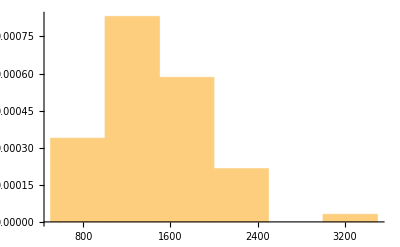

```mathematica
Histogram[CVmeans,Automatic,"PDF"]
```

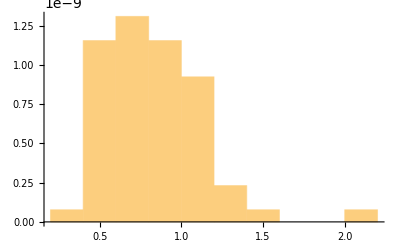

```mathematica
Histogram[CVvars,Automatic,"PDF"]
```

```mathematica
Mean[TAcmeans];
```

```mathematica
mnMns=ListPlot[{Mean[TAcmeans],TAcmeans[[1]],TAcmeans[[2]],TAcmeans[[3]]},PlotStyle->{{Black,Thick},{Red,Dashed},{Blue,Dashed},{Darker[Green],Dashed}},Joined->True];
mnVars=ListPlot[{Mean[TAcvars],TAcvars[[1]],TAcvars[[2]],TAcvars[[3]]},PlotStyle->{{Black,Thick},{Red,Dashed},{Blue,Dashed},{Darker[Green],Dashed}},Joined->True];
```

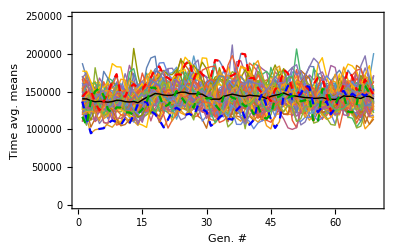

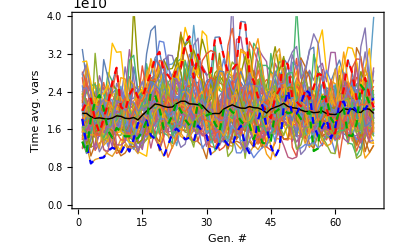

```mathematica
Show[ListPlot[AppendTo[TAcmeans,Mean[TAcmeans]],Joined->True,PlotStyle->Thin,Frame->True,FrameLabel->{"Gen. #","Time avg. means"},PlotRange->{{0,70},{0,250000}}],mnMns]
Show[ListPlot[AppendTo[TAcvars,Mean[TAcvars]],Joined->True,PlotStyle->Thin,Frame->True,FrameLabel->{"Gen. #","Time avg. vars"},PlotRange->{{0,70},{0,4*10^10}}],mnVars]
```

```mathematica
(* Fraction of lineages that are consistent with binomial partitioning with p = 1/2, i.e. they obey the relation 4*Var_after > V_before, i.e. y > 0. This is since binomial partitioning with p = 1/2 implies 4*var_after = var_before + <n>_before  *)
```

```mathematica
N[Length[data3]/Length[data1]]
```

0.553846

```mathematica
(* Using data for those lineages obeying y > 0; Linear plot with slope 1 verifies binomial partitioning with p = 1/2; the intercept is the factor g where fluorescence = g * protein number *)
```

```mathematica
lm=LinearModelFit[data3,x1,x1]
```

FittedModel[5563.24+1.06252 x1]

```mathematica
lm["RSquared"]
```

0.927442

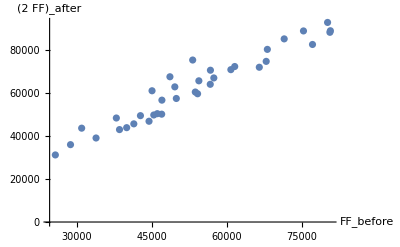

```mathematica
ListPlot[data3,PlotRange->All,AxesLabel->{Subscript[FF,before],Subscript[2*FF,after]}]
```

```mathematica
(* Ratio of protein before and after cell division for ALL lineages; a value of 2 is indication of binomial partitioning with probability of 1/2; note that the mean is greater than 2 on average showing the mother cell has more molecules after partitioning than daughter cells *)
```

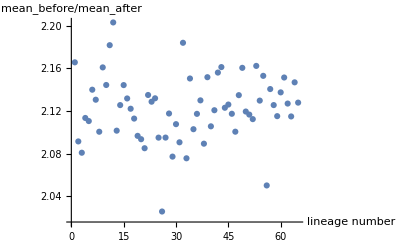

```mathematica
ListPlot[data2a,AxesLabel->{"lineage number",Subscript[mean,before]/Subscript[mean,after]}]
```

```mathematica
(* Fitting Erlang distribution of cell cycle length times; data from all lineages is pooled together *)
```

```mathematica
paramserlang=FindDistributionParameters[Flatten[CycleLength],GammaDistribution[α,β]]
```

{α→13.5223,β→5.00178}

```mathematica
N[Mean[Flatten[CycleLength]]]
```

67.6357

```mathematica
N[Variance[Flatten[CycleLength]]/Mean[Flatten[CycleLength]]^2]
```

0.0779606

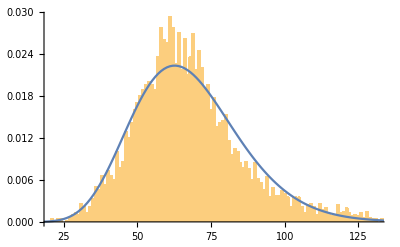

```mathematica
Show[Histogram[Flatten[CycleLength],{1},"PDF"],ListPlot[Table[{x,PDF[GammaDistribution[α,β]/.paramserlang,x]},{x,1,140}],Joined->True]]
```

```mathematica
Variance[GammaDistribution[α,β]/.{α->29.457455104443518,β->1.8143290991110723}]
```

96.9678

```mathematica
Mean[GammaDistribution[α,β]/.{α->29.457455104443518,β->1.8143290991110723}]
```

53.4455

```mathematica
(* Autocorrelation of cell cycles lengths; there are more negative correlated successive cell cycle lengths than expected by chance; correlation is 7 standard deviations away from mean and hence there is probability of 1 in 390682215445 that it can be explained by chance! however the correlation is weak *)
```

```mathematica
N[CorrelationFunction[Flatten[CycleLength],1]]
```

-0.105259

```mathematica
data4=Table[0,{i,5000}];
```

```mathematica
For[k=1,k≤5000,k++,rnddata=Table[RandomVariate[ErlangDistribution[α,β]/.paramserlang,Length[CycleLength[[i]]]],{i,Length[CycleLength]}];data4[[k]]=N[CorrelationFunction[Flatten[rnddata],1]];]
```

ErlangDistribution::pintprm: Parameter 13.5223 at position 1 in ErlangDistribution[13.5223,5.00178] is expected to be a positive integer.

General::stop: Further output of ErlangDistribution::pintprm will be suppressed during this calculation.

```mathematica
Histogram[data4]
```

-Graphics-

```mathematica
7*StandardDeviation[data4]
```

Indeterminate

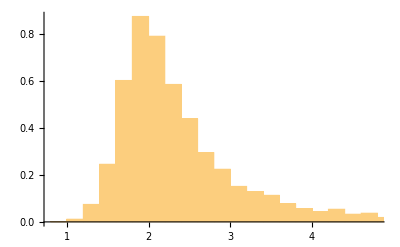

```mathematica
(* Find distribution of length increment from birth to division; does not support an adder where a constant volume is added in each cell cycle *)

Show[Histogram[Flatten[Lengthincrement],Automatic,"PDF"]]
```

```mathematica
StandardDeviation[Flatten[Lengthincrement]]/Mean[Flatten[Lengthincrement]]
```

0.37548

```mathematica
(* Find relationship between final and initial lengths *)
```

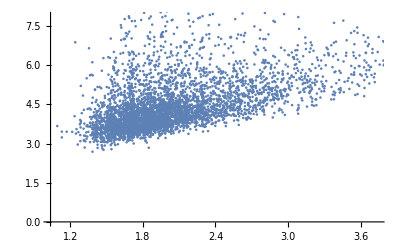

```mathematica
ListPlot[Flatten[LengthMap,1]]
```

```mathematica
lm1=LinearModelFit[Flatten[LengthMap,1],x1,x1]
```

FittedModel[2.24585+1.08987 x1]

```mathematica
lm1["RSquared"]
```

0.321985

```mathematica
(* Calculating the birth length distribution *)
```

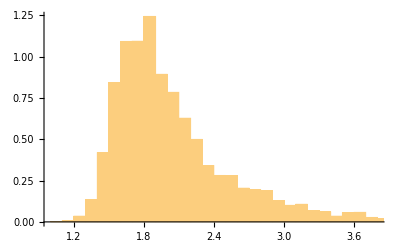

```mathematica
plbl=Histogram[Flatten[BirthLength],Automatic,"PDF"]
```

```mathematica
Mean[Flatten[BirthLength]]
```

2.07333

```mathematica
Variance[Flatten[BirthLength]]/Mean[Flatten[BirthLength]]
```

0.160303

```mathematica
parambl=FindDistributionParameters[Flatten[BirthLength],GammaDistribution[a,b]]
```

{a→16.0626,b→0.129078}

```mathematica
paramln=FindDistributionParameters[Flatten[BirthLength],LogNormalDistribution[a,b]]
```

{a→0.697703,b→0.240406}

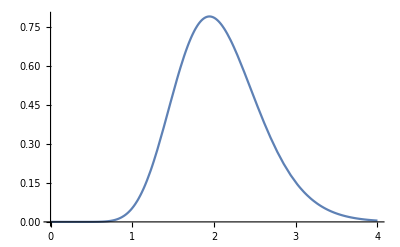

```mathematica
plgammabl=Plot[PDF[GammaDistribution[a,b]/.parambl,h],{h,0,4}]
```

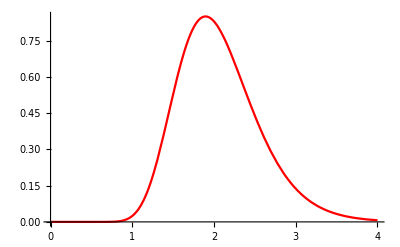

```mathematica
pllnbl=Plot[PDF[LogNormalDistribution[a,b]/.paramln,h],{h,0,4},PlotStyle->Red]
```

```mathematica
bestfitbl=PDF[FindDistribution[Flatten[BirthLength]],h]
```

Piecewise[{{0., h≤0}, {(0.253261 ⅇ^(-8.27695 (-1.09417+Log[h])^2))/h+(2.06546 ⅇ^(-18.8162 (-0.611677+Log[h])^2))/h, True}}]

General::munfl: Exp[-913.656] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1890.64] is too small to represent as a normalized machine number; precision may be lost.

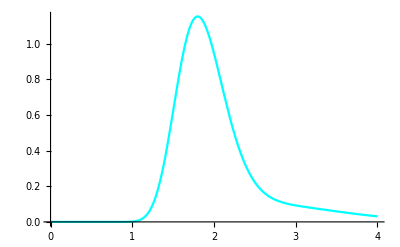

```mathematica
plmixed=Plot[bestfitbl,{h,0,4},PlotStyle->Cyan]
```

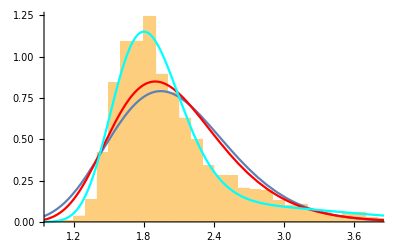

```mathematica
Show[plbl,plgammabl,pllnbl,plmixed]
```

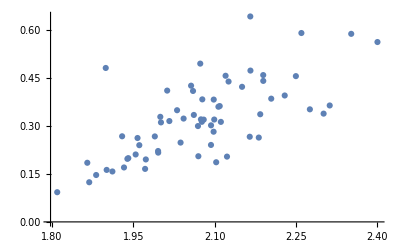

```mathematica
ListPlot[Table[{Mean[BirthLength[[i]]],Variance[BirthLength[[i]]]},{i,1,Length[BirthLength]}]]
```

```mathematica
LinearModelFit[Table[{Mean[BirthLength[[i]]],Variance[BirthLength[[i]]]},{i,1,Length[BirthLength]}],h,h]
```

FittedModel[-1.06353+0.6681 h]

```mathematica
(* The length grows exponential with cellular time; fit length vs cellular time to exponential fn and report Rsquared of plot. Mean Rsquared (calculated across cell cycles and lineages) is very close 1.  *)
```

```mathematica
Length[datA1]
```

0

```mathematica
datA1=Table[Table[Table[{i,BirthLengthCycleData[[w]][[j]][[i]]},{i,1,Length[BirthLengthCycleData[[w]][[j]]]}],{j,1,Length[BirthLengthCycleData[[w]]]}],{w,1,Length[BirthLengthCycleData]}];
```

```mathematica
datA2=Table[Table[NonlinearModelFit[datA1[[w]][[i]],a*Exp[-b*h],{a,b},h]["RSquared"],{i,1,Length[datA1]}],{w,1,Length[BirthLengthCycleData]}];
```

```mathematica
Mean[Flatten[datA2]]
```

0.99909

```mathematica
Variance[Flatten[datA2]]
```

6.81912×10^-7

```mathematica
(* The growth rate is extracted by fitting exponential fn to length vs time curves for each cell cycle in each lineage *)
```

```mathematica
datA3=Table[Table[Coefficient[FullSimplify[Log[Normal[NonlinearModelFit[datA1[[w]][[i]],a*Exp[-b*h],{a,b},h]]],Assumptions->h>0],h],{i,1,Dimensions[datA1][[2]]}],{w,1,Dimensions[datA1][[1]]}];
```

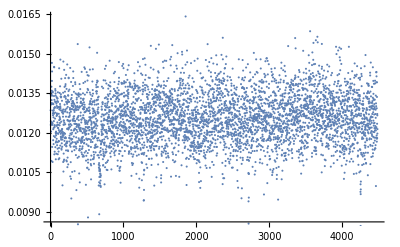

```mathematica
ListPlot[Flatten[datA3]]
```

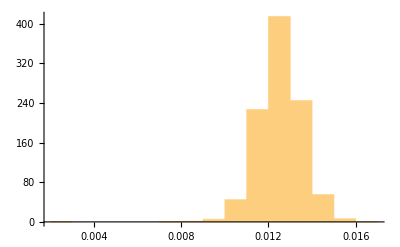

```mathematica
Histogram[Flatten[datA3],Automatic,"PDF"]
```

```mathematica
Dimensions[datA3]
```

{65,69}

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/s1402978/Desktop/Tanouchi-Inference-Project/Julia_analysis

```mathematica
datA3;
```

```mathematica
Export["exp_grs_all_25.csv",datA3,"CSV"]
```

exp_grs_all_25.csv

```mathematica
(* Calculating ratio of birth length at generation i to division length at generation i - 1 *)
```

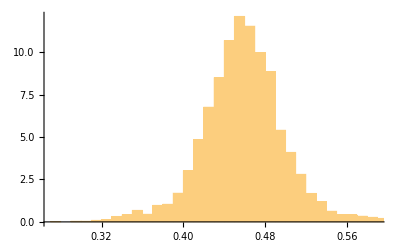

```mathematica
plratio1=Histogram[Flatten[Table[Table[BirthLength[[j]][[i+1]]/DivisionLength[[j]][[i]],{i,1,Length[BirthLength[[1]]]-1}],{j,1,Length[BirthLength]}]],Automatic,"PDF"]
```

```mathematica
Mean[Flatten[Table[Table[BirthLength[[j]][[i+1]]/DivisionLength[[j]][[i]],{i,1,Length[BirthLength[[1]]]-1}],{j,1,Length[BirthLength]}]]]
```

0.458982

```mathematica
StandardDeviation[Flatten[Table[Table[BirthLength[[j]][[i+1]]/DivisionLength[[j]][[i]],{i,1,Length[BirthLength[[1]]]-1}],{j,1,Length[BirthLength]}]]]
```

0.040667

```mathematica
paramsratio=FindDistributionParameters[Flatten[Table[Table[BirthLength[[j]][[i+1]]/DivisionLength[[j]][[i]],{i,1,Length[BirthLength[[1]]]-1}],{j,1,Length[BirthLength]}]],BetaDistribution[μ,σ]]
```

{μ→68.0802,σ→80.2445}

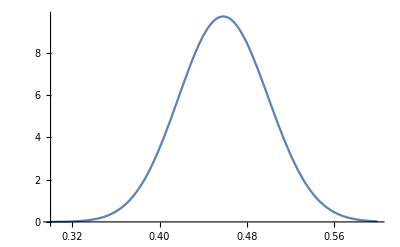

```mathematica
plratio2=Plot[PDF[BetaDistribution[μ,σ]/.paramsratio,h],{h,0.30,0.60}]
```

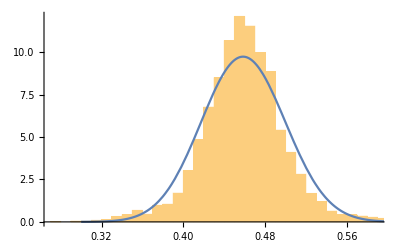

```mathematica
Show[{plratio1,plratio2}]
```

```mathematica
(* Calculating theta *)
```

```mathematica
DivisionLength[[20]]
```

{5.17121,3.91153,4.71477,4.47569,4.07255,3.94678,3.55511,3.73214,3.84417,3.49874,5.10871,5.82668,4.76074,4.12339,4.31866,4.53664,3.66462,3.20412,3.61026,3.81009,3.95262,5.48059,4.62769,4.06288,3.65581,3.93036,4.05365,3.70914,4.15974,3.62743,5.33011,6.66435,5.33129,5.27103,5.04708,4.26541,4.47323,4.25409,8.06304,6.27272,6.38795,5.54501,4.9405,7.92657,5.07784,4.98969,5.36057,5.38811,5.39889,4.71372,5.60396,4.11932,4.3349,5.52723,3.88734,4.81334,9.79959,8.5715,5.9745,5.36351,4.90516,4.175,4.28371,3.70614,3.63957,3.38609,3.36918,3.59642,3.8162}

```mathematica
BirthLength[[20]]
```

{3.3601,2.19517,1.86712,2.52718,2.00016,1.59715,1.88846,1.734,1.66347,1.89213,1.67916,3.11885,2.15267,2.23768,1.99644,2.0034,2.29685,1.65318,1.44326,1.61563,1.88156,1.63835,2.56103,2.2634,2.00049,1.56831,1.86286,1.79597,1.66183,1.74068,1.56933,2.80139,3.20059,2.6714,2.66479,2.36229,1.99202,2.26615,1.99891,3.56126,2.18499,3.04754,2.83305,2.3533,2.98094,2.3835,2.44023,3.17745,2.52173,2.59211,2.30077,2.54683,2.01749,2.04095,2.5881,1.71523,1.6595,5.70292,3.52308,2.69115,2.50366,2.28125,1.97319,2.09407,1.66183,1.54207,1.46265,1.69204,1.72713}

```mathematica
CycleLength[[20]]
```

{37,46,97,51,61,82,53,68,75,53,109,58,64,53,73,63,49,54,86,72,64,105,50,51,53,77,64,61,79,56,109,80,44,55,49,48,67,58,133,41,94,52,57,107,52,69,71,46,61,53,72,40,65,84,39,90,152,36,43,62,57,60,62,42,59,64,71,68,70}

```mathematica
Lambda=(DivisionLength[[20]]/BirthLength[[20]])
```

{1.539,1.78188,2.52516,1.77102,2.03611,2.47114,1.88254,2.15233,2.31093,1.8491,3.04242,1.86821,2.21155,1.84271,2.16318,2.26447,1.5955,1.93816,2.50146,2.35827,2.10071,3.34519,1.80696,1.79503,1.82746,2.50611,2.17604,2.06526,2.50311,2.08392,3.39642,2.37894,1.66572,1.97313,1.89399,1.80563,2.24557,1.87723,4.03372,1.76138,2.92356,1.8195,1.74388,3.36828,1.70344,2.09343,2.19675,1.69573,2.14095,1.81849,2.43569,1.61743,2.14866,2.70817,1.50201,2.80624,5.90515,1.503,1.69582,1.99302,1.9592,1.83014,2.17096,1.76983,2.1901,2.19581,2.30348,2.12549,2.20956}

```mathematica
Mean[Lambda/BirthLength[[20]]]
```

1.08084

```mathematica
Theta=1/(BirthLength[[20]]*(1 + BirthLength[[20]]/Lambda)*Log[1+Lambda/BirthLength[[20]]])
```

{0.247934,0.343445,0.359941,0.306995,0.35922,0.40675,0.382242,0.395756,0.401326,0.383173,0.371178,0.255894,0.333088,0.33594,0.354856,0.350196,0.338338,0.420775,0.436981,0.408114,0.373939,0.368295,0.30255,0.334652,0.367742,0.410792,0.373733,0.38908,0.393615,0.397652,0.378357,0.266656,0.255245,0.287529,0.290368,0.322992,0.352416,0.33132,0.302837,0.231235,0.308391,0.26203,0.280376,0.281575,0.269891,0.311221,0.302412,0.25607,0.296243,0.299244,0.309549,0.310168,0.352534,0.330833,0.310046,0.37331,0.31009,0.156349,0.234715,0.285272,0.303344,0.331268,0.357781,0.357076,0.406988,0.430258,0.44213,0.404407,0.394445}

```mathematica
Mean[Theta]
```

0.336104

```mathematica
Covariance[Theta,CycleLength[[20]]]/Mean[CycleLength[[20]]]
```

0.00522921

```mathematica
Mean[Theta]+Covariance[Theta,CycleLength[[20]]]/Mean[CycleLength[[20]]]
```

0.341333

```mathematica
Mean[Theta*CycleLength[[20]]]/Mean[CycleLength[[20]]]
```

0.341257

```mathematica
0.72/Mean[BirthLength[[20]]]
```

0.320055

```mathematica
1/Mean[Flatten[BirthLengthCycleData[[20]]]]
```

0.313909